```mathematica
ClearAll[a,M,J,θ,λ,ω,ν,r]
<<KerrWithProca`

AnalyticSolution = <|"Parameters"-><|"ϵ"->ϵ,"μNv"->μNv,"m"->m,"n"->n,"χ"->χ,"M"->M|>,"Solution"-><|"ω"->ω,"ν"->ν,"R(r)"->R,"S(θ)"->S|>|>;

$Assumptions={r>0,M>0,J>0,1>a≥0,π≥θ≥0, λ∈Complexes,ω∈Complexes, ν∈Complexes};
M=1;
SolutionPath = NotebookDirectory[]<>"Solutions/";
AllSolutions = getResults[SolutionPath];
μOrderingIndex = Ordering@AllSolutions[[All, "Parameters", "μNv"]];
AllSolutions = AllSolutions[[μOrderingIndex]];
PrepareArguments[expr_]:=expr/.θ[]->θ/.t[]->t/.ϕ[]->ϕ/.r[]->r

KerrComponents = {{-1+(2 M r)/((J^2 Cos[θ]^2)/M^2+r^2),0,0,-(2 J r*Sin[θ]^2)/((J^2 Cos[θ]^2)/M^2+r^2)},{0,(J^2 Cos[θ]^2+M^2 r^2)/(J^2+M^2 r (-2 M+r)),0,0},{0,0,(J^2 Cos[θ]^2)/M^2+r^2,0},{-(2 J r Sin[θ]^2)/((J^2 Cos[θ]^2)/M^2+r^2),0,0,Sin[θ]^2 (J^2/M^2+r^2+(2 J^2 M r Sin[θ]^2)/(J^2 Cos[θ]^2+M^2 r^2))}}/.J->a*M//FullSimplify;
IKerrComponents = Inverse[KerrComponents]//FullSimplify;

Delta = r^2-2*M*r+a^2;
Sigma = r^2+a^2*Cos[θ]^2;
qr = r^2+λ^2;
qth = λ^2-a^2*Cos[θ]^2;
(*Polarization tensor components*)
(*See arXiv:2004.09536*) 
dr = {0,1,0,0};
dt = {1,0,0,0};
dθ = {0,0,1,0};
dϕ = {0,0,0,1};
h = -(r*dr + a^2*Sin[θ]*Cos[θ]*dθ)\[TensorWedge]dt + a*Sin[θ]*(r*Sin[θ]*dr + (r^2+a^2)*Cos[θ]*dθ)\[TensorWedge]dϕ;
Bsymb = Table[Symbol["B"<>ToString[i]<>ToString[j]], {i,1,4},{j,1,4}];
sys = Bsymb.(KerrComponents + I*ν*h)//Simplify;
equ =Flatten[ Thread/@Thread[sys==DiagonalMatrix[{1,1,1,1}]]];
Coeffs = Flatten@Bsymb;
sol = Solve[equ, Coeffs, Assumptions->True]//Simplify;
PolarizationComponents = Bsymb/.sol//FullSimplify//First;

OvertoneModeGroup[nvalue_?NumberQ, mvalue_?NumberQ]:=Select[Select[AllSolutions, #["Parameters"]["n"]==nvalue&], #["Parameters"]["m"]==mvalue&]


(*https://mathematica.stackexchange.com/questions/59944/extracting-the-function-from-interpolatingfunction-object/59963#59963*)
InterpolationToPiecewise[if_,x_]:=Module[{main,default,grid},grid=if["Grid"];
Piecewise[{if@"GetPolynomial"[#,x-#],x<First@#}&/@grid[[2;;-2]],if@"GetPolynomial"[#,x-#]&@grid[[-1]]]]/;if["InterpolationMethod"]=="Hermite"

CompileInterpolating[interp_InterpolatingFunction]:=Compile[{ψ}, Evaluate[InterpolationToPiecewise[interp, ψ]]]

ParamsToReprRule[solution_]:=AssociationThread[(Symbol/@(solution[ "Parameters"]//Keys))->(solution[ "Parameters"]//Values)]//Normal

SolToReprRule[solution_]:=Block[{Rkey,Skey},
If[KeyExistsQ[solution["Solution"], "R(r)"], Rkey = "R(r)", Rkey="R"];
If[KeyExistsQ[solution["Solution"], "S(θ)"], Skey = "S(θ)", Skey="S"];
AssociationThread[{ω,ν,R,S}->Values[solution[["Solution", {"ω", "ν", Rkey, Skey}]]]]
]
HorizonCoordToRadial[xN_, χ_]:=xN*(rplusN[χ]-rminusN[χ]) + rplusN[χ];
RadialToHorizonCoord[rN_,χ_]:=(rN-rplusN[χ])/(rplusN[χ]-rminusN[χ]);

ToParamSymbols:={a->χ, λ->1/ν};

ApplySolutionSet[solution_][expr_]:= expr/.ToParamSymbols/.ParamsToReprRule[solution]/.SolToReprRule[solution];

ToXACTSymbol[expr_]:=expr/.{t->t[], r->r[], θ->θ[], ϕ->ϕ[]}
FromXACTSymbol[expr_]:=expr/.{t[]->t,r[]->r, θ[]->θ, ϕ[]-> ϕ}
ApplyParameters[solution_][expr_]:=expr/.{a->solution[["Parameters","χ"]], λ-> 1/solution[["Solution", "ν"]], m-> solution[["Parameters", "m"]], n-> solution[["Parameters", "n"]]}





FKKSZ[solution_]:=
Block[{Rkey,Skey},
If[KeyExistsQ[solution["Solution"], "R(r)"], Rkey = "R(r)", Rkey="R"];
If[KeyExistsQ[solution["Solution"], "S(θ)"], Skey = "S(θ)", Skey="S"];
Block[{ww = solution[["Solution", "ω"]], 
 	mm = solution[["Parameters", "m"]],
 	Sinterp = solution[["Solution", Skey]], 
 	Rinterp = Evaluate@Function[{r},Evaluate@solution[["Solution",Rkey]][RadialToHorizonCoord[r,solution[["Parameters","χ"]]]]],
 	res
	},
res = Exp[-I*ww*t]*Rinterp[r]*Sinterp[θ]*Exp[I*mm*ϕ];
{t,r,θ,ϕ}↦ Evaluate[res]
]
];
FKKSProca[U][solution_]:=
Block[{FKKSs, res,AnalyticRes},
If[FileExistsQ[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSProcaU.mx"}]],
(*True*)
AnalyticRes = Import[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSProcaU.mx"}]];,

(*False*)
FKKSs = FKKSZ[AnalyticSolution][t,r,θ,ϕ];
AnalyticRes =Simplify[PolarizationComponents.(D[(FKKSs), {{t,r,θ,ϕ},1}])]//ApplySolutionSet[solution];
Export[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSProcaU.mx"}], AnalyticRes];
];
res = AnalyticRes//ApplySolutionSet[solution];
{t,r,θ,ϕ}↦ Evaluate[res]
]

FKKSProca[L][solution_]:=
Block[{tmp,res,g,AnalyticRes},
If[FileExistsQ[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSProcaL.mx"}]],
(*True*)
AnalyticRes = Import[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSProcaL.mx"}]];,

(*False*)
g=KerrComponents;
tmp = FKKSProca[U][AnalyticSolution][t,r,θ,ϕ];
AnalyticRes =Simplify[g.tmp];
Export[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSProcaL.mx"}], AnalyticRes];
];
res = AnalyticRes//ApplySolutionSet[solution];
{t,r,θ,ϕ}↦ Evaluate[res]
]

FKKSFieldStrength::usage="Computes field strength tensor of proca field for various index structures";
FKKSFieldStrength[LL][solution_]:=
Block[{tmp, res,AnalyticRes},
If[FileExistsQ[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSFieldStrengthLL.mx"}]],
(*True*)
AnalyticRes = Import[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSFieldStrengthLL.mx"}]];,

(*False*)
tmp =  Transpose[D[(FKKSProca[L][AnalyticSolution][t,r,θ,ϕ]), {{t,r,θ,ϕ},1}]];
AnalyticRes = Simplify[Rationalize[tmp - Transpose[tmp],0], TimeConstraint->Infinity];
Export[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSFieldStrengthLL.mx"}], AnalyticRes];
];
res = AnalyticRes//ApplySolutionSet[solution];
{t,r,θ,ϕ}↦Evaluate[res]
]

FKKSFieldStrength[UU][solution_]:=
Block[{tmp,res,ig, AnalyticRes},
If[FileExistsQ[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSFieldStrengthUU.mx"}]],
(*true*)
AnalyticRes = Import[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSFieldStrengthUU.mx"}]];,

(*false*)
ig = Simplify[IKerrComponents];
tmp = FKKSFieldStrength[LL][AnalyticSolution][t,r,θ,ϕ];
AnalyticRes = Simplify[ig.tmp.Transpose[ig], TimeConstraint->Infinity];
Export[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSFieldStrengthUU.mx"}], AnalyticRes];
];
res = AnalyticRes//ApplySolutionSet[solution];
{t,r,θ,ϕ}↦Evaluate[res]
]

FKKSFieldStrength[UL][solution_]:=
Block[{tmp,res,ig,AnalyticRes},
If[FileExistsQ[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSFieldStrengthUL.mx"}]],
(*true*)
AnalyticRes = Import[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSFieldStrengthUL.mx"}]];,

(*false*)
ig = Simplify[IKerrComponents];
tmp = FKKSFieldStrength[LL][AnalyticSolution][t,r,θ,ϕ];
AnalyticRes = Simplify[ig.tmp, TimeConstraint->Infinity];
Export[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSFieldStrengthUL.mx"}], AnalyticRes];
];
res = AnalyticRes//ApplySolutionSet[solution];
{t,r,θ,ϕ}↦Evaluate[res]
]


FKKSEnergyMomentum::usage="Compute Energy Momentum tensor for given solution set for various index structures.";
FKKSEnergyMomentum[UU][solution_, OutputForm_:<|"SymbolicExpression"->False|>]:=
Block[{Tll,res,g,AnalyticRes, OptimizedResult, resOE,ig},
If[FileExistsQ[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSEnergyMomentumUU.mx"}]],
(*true*)
AnalyticRes = Import[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSEnergyMomentumUU.mx"}]];,

(*false*)
ig = Simplify@IKerrComponents;
Tll = FKKSEnergyMomentum[LL][AnalyticSolution, <|"SymbolicExpression"->True|>][t,r,θ,ϕ];
AnalyticRes = ig.Tll.ig;
Export[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSEnergyMomentumUU.mx"}], AnalyticRes];
];
res = AnalyticRes//ApplySolutionSet[solution];
resOE = Experimental`OptimizeExpression[res, OptimizationSymbol->a];

OptimizedResult = resOE/.Experimental`OptimizedExpression[f_]:>Function@@Hold[{t,r,θ,ϕ}, f];
If[OutputForm["SymbolicExpression"], {t,r,θ,ϕ}|-> Evaluate[res], OptimizedResult]
]

FKKSEnergyMomentum[UL][solution_, OutputForm_:<|"SymbolicExpression"->False|>]:=
Block[{Tll,res,g,AnalyticRes, OptimizedResult, resOE,ig},
If[FileExistsQ[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSEnergyMomentumUL.mx"}]],
(*true*)
AnalyticRes = Import[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSEnergyMomentumUL.mx"}]];,

(*false*)
ig = Simplify@IKerrComponents;
Tll = FKKSEnergyMomentum[LL][AnalyticSolution, <|"SymbolicExpression"->True|>][t,r,θ,ϕ];
AnalyticRes = ig.Tll;
Export[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSEnergyMomentumUL.mx"}], AnalyticRes];
];
res = AnalyticRes//ApplySolutionSet[solution];
resOE = Experimental`OptimizeExpression[res, OptimizationSymbol->a];

OptimizedResult = resOE/.Experimental`OptimizedExpression[f_]:>Function@@Hold[{t,r,θ,ϕ}, f];
If[OutputForm["SymbolicExpression"], {t,r,θ,ϕ}|-> Evaluate[res], OptimizedResult]
]

FKKSEnergyMomentum[LL][solution_, OutputForm_:<|"SymbolicExpression"->False|>]:=
Block[{tmp,res,Fll,Fuu,Ful,Flu, Al,Au,ig,g,μ, AnalyticRes,OptimizedResult, resOE},
If[FileExistsQ[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSEnergyMomentumLL.mx"}]],
(*true*)
AnalyticRes = Import[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSEnergyMomentumLL.mx"}]];,

(*false*)
μ=solution["Parameters", "μNv"]*M;
ig = Simplify@IKerrComponents;
g = Simplify@KerrComponents;
Fll = FKKSFieldStrength[LL][AnalyticSolution][t,r,θ,ϕ];
Ful = FKKSFieldStrength[UL][AnalyticSolution][t,r,θ,ϕ];
Flu = -Transpose[Ful];
Fuu = FKKSFieldStrength[UU][AnalyticSolution][t,r,θ,ϕ];
Al=FKKSProca[L][AnalyticSolution][t,r,θ,ϕ];
Au = FKKSProca[U][AnalyticSolution][t,r,θ,ϕ];
(*AnalyticRes = (-1/4 ig*Tr[Fll.Fuu] -Fuu.g.Fuu + μ^2/2 ig*Al.Au +μ^2*Au⊗Au);*)
T1 = Table[Sum[Fll[[μ,λ]]*Flu[[ν,λ]], {λ,1,4}], {μ,1,4},{ν,1,4}];(*Subscript[F, μλ] Subscript[F, ν]^λ*)
T2 = μ^2*Al⊗Al;(*μ^2 Subscript[A, μ] Subscript[A, ν]*)
T3 = -1/4 Table[Sum[g[[μ,ν]]*Fll[[λ,γ]]*Fuu[[λ,γ]], {λ,1,4},{γ,1,4}], {μ,1,4},{ν,1,4}];(*-1/4 Subscript[g, μν] Subscript[F, λγ] F^λγ*)
T4 = -1/2*μ^2*Table[g[[μ,ν]]*(Al.Au), {μ,1,4},{ν,1,4}];(*-1/2 μ^2 Subscript[g, μν] Subscript[A, λ] A^λ*)
AnalyticRes = (T1+T2+T3+T4); (*S&E expression*)
Export[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSEnergyMomentumLL.mx"}], AnalyticRes];
];
res = AnalyticRes//ApplySolutionSet[solution];
resOE = Experimental`OptimizeExpression[res, OptimizationSymbol->a];

OptimizedResult = resOE/.Experimental`OptimizedExpression[f_]:>Function@@Hold[{t,r,θ,ϕ}, f];
If[OutputForm["SymbolicExpression"], {t,r,θ,ϕ}|-> Evaluate[res], OptimizedResult]
]

FKKSEnergyDensity[solution_, OutputForm_:<|"SymbolicExpression"->False|>]:=
Block[{AnalyticRes, res, resOE, OptimizedResult},
If[FileExistsQ[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSEnergyDensity.mx"}]],
(*true*)
AnalyticRes = Import[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSEnergyDensity.mx"}]];,

(*false*)
AnalyticRes = -FKKSEnergyMomentum[UL][AnalyticSolution, <|"SymbolicExpression"->True|>][t,r,θ,ϕ]//First//First;
Export[FileNameJoin[{NotebookDirectory[], "Expressions", "FKKSEnergyDensity.mx"}], AnalyticRes];
];
res = AnalyticRes//ApplySolutionSet[solution];
resOE = Experimental`OptimizeExpression[res, OptimizationSymbol->a];

OptimizedResult = resOE/.Experimental`OptimizedExpression[f_]:>Function@@Hold[{t,r,θ,ϕ}, f];
If[OutputForm["SymbolicExpression"], {t,r,θ,ϕ}|-> Evaluate[res], OptimizedResult]
]
```

```mathematica
OvertoneModeGroup[nvalue_?NumberQ, mvalue_?NumberQ]:=Select[Select[AllSolutions, #["Parameters"]["n"]==nvalue&], #["Parameters"]["m"]==mvalue&]
```

```mathematica
testsol = getResults[SolutionPath, {{"m",1},{"n",0},{"branch",1}, {"μNv","1_5"}}]//First;
```

0.195612573304216953+6.4294954016241731×10^-6 ⅈ

InterpolatingFunction[…]

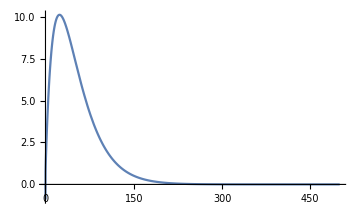
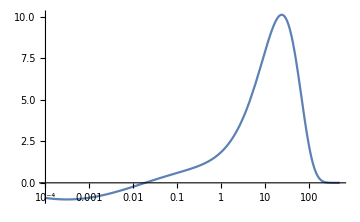

```mathematica
solw = testsol[["Solution", "ω"]]
solr = testsol[["Solution", "R"]]
Row[{Plot[solr[r]//Re, {r,0.001, solr["Domain"]//First//Last}, PlotRange->All, ImageSize->Medium],
LogLinearPlot[solr[r]//Re, {r,0.0001,  solr["Domain"]//First//Last}, ImageSize->Medium]}]
```

```mathematica
tmp = FKKSEnergyDensity[testsol];
tmp1 = FKKSEnergyMomentum[LL][testsol];
Row[{Plot[tmp[0,r,π/2,0]//Re, {r,1.44, 20}, PlotRange->All, ImageSize->Medium],
Plot[-tmp1[0,r,1,0][[1,1]]//Re, {r,1.44, 20}, PlotRange->All, ImageSize->Medium]}]
(*Row[{Plot[tmp[0,r,π/2,0]//Re, {r,1.44,  solr["Domain"]//First//Last}, PlotRange->All, ImageSize->Medium],
Plot[-tmp1[0,r,1,0][[1,1]]//Re, {r,1.44,  solr["Domain"]//First//Last}, PlotRange->All, ImageSize->Medium]}]*)
```

```mathematica
Plot3D[tmp[0,r,θ,0]//Re, {r,1.44, 250},{θ,0,π}, PlotRange->{0,All}]
LogLinearPlot[tmp[0,HorizonCoordToRadial[x,9/10],π/2,0]//Re, {x,0.001,250}, PlotRange->All]
```

```mathematica
NIntegrate[tmp[0,r,θ,ϕ]//Re, {r,1.44,250}, {θ,0,π},{ϕ,0,2*π}, Method->{"GlobalAdaptive" , "MaxErrorIncreases"->10^6}]
```

```mathematica
μ=testsol["Parameters", "μNv"]*M;
ig = Simplify@IKerrComponents;
g = Simplify@KerrComponents;
Fll = FKKSFieldStrength[LL][AnalyticSolution][t,r,θ,ϕ];
Ful = FKKSFieldStrength[UL][AnalyticSolution][t,r,θ,ϕ];
Flu = -Transpose[Ful];
Fuu = FKKSFieldStrength[UU][AnalyticSolution][t,r,θ,ϕ];
Al=FKKSProca[L][AnalyticSolution][t,r,θ,ϕ];
Au = FKKSProca[U][AnalyticSolution][t,r,θ,ϕ];
T1 = Ful[[1,All]].Flu[[1,All]];
T2 = μ^2*Au[[1]]*Al[[1]];
T3 = -1/4*Tr[Fll.Transpose[Fuu]];
T4 = -1/2*μ^2*(Al.Au);
ρTilde = -(T1+T2+T3+T4);
```

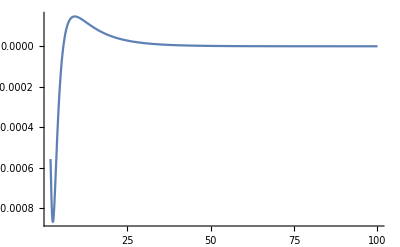

```mathematica
rhoT = Function[{t,r,θ,ϕ},Evaluate@(ρTilde//ApplySolutionSet[testsol])];
tp = FKKSEnergyDensity[testsol][0,r,π/2,0]-(rhoT[0,r,π/2,0]);
Plot[tp//Re,{r,2,100}, PlotRange->All]
```

```mathematica
Plot3D[rhoT[0,r,θ,0]//Re, {r,2,40}, {θ,3 π/4,π}]
```

-Graphics3D-

```mathematica
sol1 = FKKSProca[U][AnalyticSolution][t,r,θ,ϕ];

FKKSs = FKKSZ[AnalyticSolution][t,r,θ,ϕ];
sol2 =Simplify[PolarizationComponents.D[(FKKSs), {{t,r,θ,ϕ},1}]]//ApplySolutionSet[AnalyticSolution];
```

```mathematica
Simplify[sol1-sol2]
```

```mathematica
ClearAll[χ,m,ω]
sol2[[2]]//Simplify;
NSproca = {-((ⅈ ⅇ^(-ⅈ (-m ϕ+t ω)) (-1/2 r ν (-2 r^3+r^4-2 r χ^2+2 r^2 χ^2+χ^4) (-2+ν^2 χ^2+ν^2 χ^2 Cos[2 θ]) S[θ] f'[r]+f[r] ((r (m χ (-2-2 r^2 ν^2+r^3 ν^2+r ν^2 χ^2)+(r^3+2 χ^2+r χ^2+2 r^2 ν^2 χ^2-r^3 ν^2 χ^2-r ν^2 χ^4) ω)+χ^2 (m ν^2 χ (r^2+χ^2)+(-2 r+r^2-2 r^3 ν^2+χ^2-r^2 ν^2 χ^2-ν^2 χ^4) ω) Cos[θ]^2) S[θ]+ν (1+r^2 ν^2) χ^2 (-2 r+r^2+χ^2) Cos[θ] Sin[θ] S'[θ])))/((1+r^2 ν^2) (-2 r+r^2+χ^2) (r^2+χ^2 Cos[θ]^2) (-1+ν^2 χ^2 Cos[θ]^2))),(ⅇ^(-ⅈ (-m ϕ+t ω)) S[θ] (r ν (m χ-(r^2+χ^2) ω) f[r]+(-2 r+r^2+χ^2) f'[r]))/((1+r^2 ν^2) (r^2+χ^2 Cos[θ]^2)),-(ⅇ^(-ⅈ (-m ϕ+t ω)) f[r] (ν χ S[θ] (m Cot[θ]-χ ω Cos[θ] Sin[θ])+S'[θ]))/((r^2+χ^2 Cos[θ]^2) (-1+ν^2 χ^2 Cos[θ]^2)),(ⅈ ⅇ^(-ⅈ (-m ϕ+t ω)) (1/2 r ν χ (-2 r+r^2+χ^2) (-2+ν^2 χ^2+ν^2 χ^2 Cos[2 θ]) S[θ] f'[r]+f[r] ((r χ (-2-2 r^2 ν^2+r^3 ν^2+r ν^2 χ^2) ω-m χ^2 (1+ν^2 χ^2) Cot[θ]^2+ν^2 χ^3 Cos[θ]^2 ((r^2+χ^2) ω+m χ Cot[θ]^2)-m r (-2+r-2 r^2 ν^2+r^3 ν^2+r ν^2 χ^2) Csc[θ]^2) S[θ]-ν (1+r^2 ν^2) χ (-2 r+r^2+χ^2) Cot[θ] S'[θ])))/((1+r^2 ν^2) (-2 r+r^2+χ^2) (r^2+χ^2 Cos[θ]^2) (-1+ν^2 χ^2 Cos[θ]^2))};
(sol2-NSproca)/.f[r_]-> R[(-1+r-√(1-χ^2))/(2 √(1-χ^2))]/.f'[r_]-> R'[(-1+r-√(1-χ^2))/(2 √(1-χ^2))]/(2 √(1-χ^2))//Simplify
```

```mathematica
sol
```

```mathematica
KerrComponents.IKerrComponents//FullSimplify
```

```mathematica
With[{fun = FKKSEnergyDensity[AllSolutions[[1]]]},
DensityPlot3D[fun[0,Norm[{x,y,z}],ArcCos[z/Norm[{x,y,z}]],ArcTan[y/x]]//Abs,{x,-1000,1000},{y,0,1000},{z,-1000,1000}]
]
```